```mathematica
(*css zebrafinch model*)
(*recursions*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs(lsI vI z +lsO qO + lsV qV) + nh vh(lhI vI z +lhO qO + lhV qV);
NNn :=ns vs(lsI vI (1-z)+lsO(1- qO) + lsV (1-qV)) + nh vh(lhI vI (1-z)+lhO(1- qO) + lhV(1- qV));
qO := (1-u)(Na/(Na +Nn));
qV:= (1-u)(Na ba/(Na ba +Nn bn));
```

```mathematica
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs(lsI vI z +lsO qO + lsV qV), vh(lhI vI z +lhO qO + lhV qV), 0, 0}, {vs(lsI vI (1-z)+lsO(1- qO) + lsV (1-qV)), vh(lhI vI (1-z)+lhO(1- qO) + lhV(1- qV)), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
Fasols=Solve[FFa==Fa,Fa]
```

{{Fa→-(-ba^2 lhV vh+3 ba bn lhV vh-2 bn^2 lhV vh+ba^2 lhV pa vh-ba bn lhV pa vh-2 ba bn lhV pn vh+2 bn^2 lhV pn vh+2 ba bn lhO u vh-2 bn^2 lhO u vh+41+ba^2 lhI pa vh vI z-ba bn lhI pa vh vI z-ba bn lhI pn vh vI z+bn^2 lhI pn vh vI z-ba^2 lsI pa vI vs z+ba bn lsI pa vI vs z+ba bn lsI pn vI vs z-bn^2 lsI pn vI vs z)/(3 (ba^2 lhV vh-2 ba bn lhV vh+bn^2 lhV vh-ba^2 lhV pa vh+ba bn lhV pa vh+ba bn lhV pn vh-bn^2 lhV pn vh+ba^2 lhO u vh-2 ba bn lhO u vh+22+bn^2 lsV pn vs+ba^2 lsO pa u vs-ba bn lsO pa u vs-ba bn lsO pn u vs+bn^2 lsO pn u vs+ba^2 lsI pa vI vs-ba bn lsI pa vI vs-ba bn lsI pn vI vs+bn^2 lsI pn vI vs))-1/1+(1)^(1/3)/(3 2^1 (1))},{Fa→1},{Fa→1}}
 |  |  |  |

```mathematica
subtest = {ba->3,bn->1,z->0.8,pa->0,pn->1,vs->0.8,vh->0.95,vI->0.7  ,lsO-> 0.5 ,lsV-> 0.1,lhO-> 0.5,lhV-> 0.1,  lhI-> 0.4, lsI->0.4,u-> 0.05 };
```

```mathematica
Fasols/.subtest (*check it is stable qhat with values, select positive q-hat*)
Fasols[[1,1,2]]/.subtest
```

{{Fa→0.765973+0. ⅈ},{Fa→-0.390244+5.55112×10^-17 ⅈ},{Fa→-0.361035-5.55112×10^-17 ⅈ}}

0.765973+0. ⅈ

```mathematica
Fasols[[1,1,2]]/.{lhO->LHO,lhV -> LHV, lsO -> LSO, lsV-> LSV,lsI -> LSI, lhI-> LHI}/.{pa->0, pn-> 1}(*copy and paste solution below*)
```

-((-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)/(3 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs)))-(2^(1/3) (-(-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^2+3 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z)))/(3 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) ((27 bn^2 LSI vI vs (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs)^2 z-2 (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^3+9 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z)+√(4 (-(-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^2+3 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z))^3+(27 bn^2 LSI vI vs (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs)^2 z-2 (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^3+9 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z))^2)))^(1/3))+((27 bn^2 LSI vI vs (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs)^2 z-2 (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^3+9 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z)+√(4 (-(-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^2+3 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z))^3+(27 bn^2 LSI vI vs (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs)^2 z-2 (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^3+9 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z))^2)))^(1/3)/(3 2^(1/3) (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs))

$Aborted

```mathematica
(*make QHAT a function of css states*)
```

```mathematica
QHAT[LHO_,LSO_,LHV_,LSV_,LSI_,LHI_] :=-((-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)/(3 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs)))-(2^(1/3) (-(-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^2+3 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z)))/(3 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) ((27 bn^2 LSI vI vs (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs)^2 z-2 (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^3+9 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z)+√(4 (-(-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^2+3 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z))^3+(27 bn^2 LSI vI vs (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs)^2 z-2 (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^3+9 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z))^2)))^(1/3))+((27 bn^2 LSI vI vs (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs)^2 z-2 (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^3+9 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z)+√(4 (-(-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^2+3 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z))^3+(27 bn^2 LSI vI vs (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs)^2 z-2 (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z)^3+9 (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs) (-ba^2 LHV vh+ba bn LHV vh+ba bn LHO u vh+ba^2 LHV u vh+ba bn LHI vh vI+2 ba bn LSV vs-2 bn^2 LSV vs+ba bn LSO u vs-2 bn^2 LSO u vs-ba bn LSV u vs+ba bn LSI vI vs-2 bn^2 LSI vI vs-ba^2 LHI vh vI z+ba bn LHI vh vI z+ba bn LSI vI vs z-bn^2 LSI vI vs z) (-ba bn LSV vs+bn^2 LSV vs+bn^2 LSO u vs+ba bn LSV u vs+bn^2 LSI vI vs-ba bn LHI vh vI z-ba bn LSI vI vs z+2 bn^2 LSI vI vs z))^2)))^(1/3)/(3 2^(1/3) (ba^2 LHV vh-ba bn LHV vh+ba^2 LHO u vh-ba bn LHO u vh+ba^2 LHI vh vI-ba bn LHI vh vI-ba bn LSV vs+bn^2 LSV vs-ba bn LSO u vs+bn^2 LSO u vs-ba bn LSI vI vs+bn^2 LSI vI vs));
```

```mathematica
AA2=AA/.{Na->Qh,Nn->(1-Qh)}/.{pa->0, pn->1};
```

```mathematica
LL=Eigenvalues[AA2];
```

```mathematica
(*LV=Eigenvectors[AA2]*);
```

Eigenvectors::eivec0: Unable to find all eigenvectors.

```mathematica
LL/.subtest /. Qh -> 0.5 (*sub in rando qhat value to identify positive eigen values*)
```

{1.49012×10^-8,-1.49012×10^-8,1.3402,-1.3402}

```mathematica
(*eigenvectors give one ratios of stage/stress classes*) 
LV/.subtest /. Qh -> 0.5
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Simplify[LL[[3]]]
```

-1/(√2 (bn (-1+Qh)-ba Qh))(√(ba bn^2 lhO Qh vh+ba^2 bn lhV Qh vh+2 ba^2 bn lhO Qh^2 vh-2 ba bn^2 lhO Qh^2 vh+ba^3 lhV Qh^2 vh-ba^2 bn lhV Qh^2 vh+ba^3 lhO Qh^3 vh-2 ba^2 bn lhO Qh^3 vh+ba bn^2 lhO Qh^3 vh-ba bn^2 lhO Qh u vh-ba^2 bn lhV Qh u vh-2 ba^2 bn lhO Qh^2 u vh+2 ba bn^2 lhO Qh^2 u vh-ba^3 lhV Qh^2 u vh+ba^2 bn lhV Qh^2 u vh-ba^3 lhO Qh^3 u vh+2 ba^2 bn lhO Qh^3 u vh-ba bn^2 lhO Qh^3 u vh+bn^3 lsO vs+bn^3 lsV vs+2 ba bn^2 lsO Qh vs-3 bn^3 lsO Qh vs+ba bn^2 lsV Qh vs-2 bn^3 lsV Qh vs+ba^2 bn lsO Qh^2 vs-4 ba bn^2 lsO Qh^2 vs+3 bn^3 lsO Qh^2 vs-ba bn^2 lsV Qh^2 vs+bn^3 lsV Qh^2 vs-ba^2 bn lsO Qh^3 vs+2 ba bn^2 lsO Qh^3 vs-bn^3 lsO Qh^3 vs+bn^3 lsO Qh u vs+ba bn^2 lsV Qh u vs+2 ba bn^2 lsO Qh^2 u vs-2 bn^3 lsO Qh^2 u vs+ba^2 bn lsV Qh^2 u vs-ba bn^2 lsV Qh^2 u vs+ba^2 bn lsO Qh^3 u vs-2 ba bn^2 lsO Qh^3 u vs+bn^3 lsO Qh^3 u vs+bn^3 lsI vI vs+2 ba bn^2 lsI Qh vI vs-2 bn^3 lsI Qh vI vs+ba^2 bn lsI Qh^2 vI vs-2 ba bn^2 lsI Qh^2 vI vs+bn^3 lsI Qh^2 vI vs+ba bn^2 lhI vh vI z+2 ba^2 bn lhI Qh vh vI z-2 ba bn^2 lhI Qh vh vI z+ba^3 lhI Qh^2 vh vI z-2 ba^2 bn lhI Qh^2 vh vI z+ba bn^2 lhI Qh^2 vh vI z-bn^3 lsI vI vs z-2 ba bn^2 lsI Qh vI vs z+2 bn^3 lsI Qh vI vs z-ba^2 bn lsI Qh^2 vI vs z+2 ba bn^2 lsI Qh^2 vI vs z-bn^3 lsI Qh^2 vI vs z+√((bn+ba Qh-bn Qh)^2 (bn^4 (-1+Qh)^2 vs^2 (lsO+lsV+lsO Qh (-1+u)-lsI vI (-1+z))^2+ba^4 Qh^2 vh^2 (lhV-lhV u+lhO (Qh-Qh u)+lhI vI z)^2-2 ba bn^3 (-1+Qh) vs (2 lhI lsO Qh vh vI-2 lhI lsO Qh^2 vh vI-2 lhI lsO Qh u vh vI+2 lhI lsO Qh^2 u vh vI+lsO^2 Qh vs+lsO lsV Qh vs-2 lsO^2 Qh^2 vs-lsO lsV Qh^2 vs+lsO^2 Qh^3 vs+lsO lsV Qh u vs+lsV^2 Qh u vs+2 lsO^2 Qh^2 u vs-2 lsO^2 Qh^3 u vs+lsO lsV Qh^2 u^2 vs+lsO^2 Qh^3 u^2 vs+2 lsI lsO Qh vI vs+lsI lsV Qh vI vs-2 lsI lsO Qh^2 vI vs+lsI lsV Qh u vI vs+2 lsI lsO Qh^2 u vI vs+lsI^2 Qh vI^2 vs-lhI lsO vh vI z-lhI lsV vh vI z+lhI lsV Qh vh vI z+lhI lsO Qh^2 vh vI z+lhI lsO Qh u vh vI z-lhI lsO Qh^2 u vh vI z+lhI lsI vh vI^2 z-lhI lsI Qh vh vI^2 z-2 lsI lsO Qh vI vs z-lsI lsV Qh vI vs z+2 lsI lsO Qh^2 vI vs z-lsI lsV Qh u vI vs z-2 lsI lsO Qh^2 u vI vs z-2 lsI^2 Qh vI^2 vs z-lhI lsI vh vI^2 z^2+lhI lsI Qh vh vI^2 z^2+lsI^2 Qh vI^2 vs z^2+2 lhV (-1+Qh) vh (lsO Qh (-1+u)-lsI vI z)+lhO (-1+Qh) vh (lsO Qh (1+Qh (-1+u)) (-1+u)+lsV (Qh-Qh u)+lsI vI (-2 z-Qh (-1+u) (1+z))))-2 ba^3 bn Qh vh (lhO^2 (-1+Qh) Qh^2 (-1+u)^2 vh+lhO Qh (lhV (-1+Qh) (-1+u)^2 vh-lsO Qh vs+lsO Qh^2 vs+lsV (2+Qh (-2+u)) (-1+u) vs+lsO Qh u vs-2 lsO Qh^2 u vs+lsO Qh^2 u^2 vs+lsI Qh vI vs-lsI Qh u vI vs-2 lhI vh vI z+2 lhI Qh vh vI z+2 lhI u vh vI z-2 lhI Qh u vh vI z-2 lsI vI vs z+lsI Qh vI vs z-lsI Qh u vI vs z)+lhI vI (lsO Qh vs (-Qh (-1+u) (-2+z)+z)+lsV Qh vs (-2+2 u+2 z-u z)+vI z (lsI Qh vs (-1+z)+lhI (-1+Qh) vh z))+lhV (lsV Qh (-1+u) u vs+lsO Qh (-1+u) (-1+Qh+Qh u) vs-vI (lhI (-1+Qh) (-1+u) vh z+lsI Qh vs (-1+u+z+u z))))+ba^2 bn^2 (lhO^2 (-1+Qh)^2 Qh^2 (-1+u)^2 vh^2+4 lhI lsV Qh vh vI vs+8 lhI lsO Qh^2 vh vI vs-4 lhI lsV Qh^2 vh vI vs-8 lhI lsO Qh^3 vh vI vs-4 lhI lsV Qh u vh vI vs-8 lhI lsO Qh^2 u vh vI vs+4 lhI lsV Qh^2 u vh vI vs+8 lhI lsO Qh^3 u vh vI vs+lsO^2 Qh^2 vs^2-2 lsO^2 Qh^3 vs^2+lsO^2 Qh^4 vs^2+2 lsO lsV Qh^2 u vs^2+2 lsO^2 Qh^3 u vs^2-2 lsO lsV Qh^3 u vs^2-2 lsO^2 Qh^4 u vs^2+lsV^2 Qh^2 u^2 vs^2+2 lsO lsV Qh^3 u^2 vs^2+lsO^2 Qh^4 u^2 vs^2+2 lsI lsO Qh^2 vI vs^2-2 lsI lsO Qh^3 vI vs^2+2 lsI lsV Qh^2 u vI vs^2+2 lsI lsO Qh^3 u vI vs^2+lsI^2 Qh^2 vI^2 vs^2-4 lhI lsO Qh vh vI vs z-6 lhI lsV Qh vh vI vs z+6 lhI lsV Qh^2 vh vI vs z+4 lhI lsO Qh^3 vh vI vs z+2 lhI lsV Qh u vh vI vs z+4 lhI lsO Qh^2 u vh vI vs z-2 lhI lsV Qh^2 u vh vI vs z-4 lhI lsO Qh^3 u vh vI vs z+4 lhI lsI Qh vh vI^2 vs z-4 lhI lsI Qh^2 vh vI^2 vs z-2 lsI lsO Qh^2 vI vs^2 z+2 lsI lsO Qh^3 vI vs^2 z-2 lsI lsV Qh^2 u vI vs^2 z-2 lsI lsO Qh^3 u vI vs^2 z-2 lsI^2 Qh^2 vI^2 vs^2 z+lhI^2 vh^2 vI^2 z^2-2 lhI^2 Qh vh^2 vI^2 z^2+lhI^2 Qh^2 vh^2 vI^2 z^2-4 lhI lsI Qh vh vI^2 vs z^2+4 lhI lsI Qh^2 vh vI^2 vs z^2+lsI^2 Qh^2 vI^2 vs^2 z^2+2 lhV (-1+Qh) Qh vh vs (lsV (-1+u)+lsO (-1+u) (-1+Qh (3+u))-lsI vI (-1+u+3 z+u z))+2 lhO (-1+Qh) Qh vh (lsV (2+Qh (-3+u)) (-1+u) vs+2 lsO Qh (1+Qh (-1+u)) (-1+u) vs+vI (lhI (-1+Qh+u-Qh u) vh z-2 lsI vs (2 z+Qh (-1+u) (1+z)))))))))

```mathematica
(*isolate dominant eigenvalue*)
Lambda[ lsO_, lhO_,LHO_,LSO_,lsI_, lhI_,LHI_,LSI_,lsV_, lhV_,LHV_,LSV_]:=-1/(√2 (bn (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV])-ba QHAT[LSO,LHO,LSI,LHI,LSV,LHV]))(√(ba bn^2 lhO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh+ba^2 bn lhV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh+2 ba^2 bn lhO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh-2 ba bn^2 lhO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh+ba^3 lhV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh-ba^2 bn lhV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh+ba^3 lhO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 vh-2 ba^2 bn lhO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 vh+ba bn^2 lhO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 vh-ba bn^2 lhO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vh-ba^2 bn lhV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vh-2 ba^2 bn lhO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vh+2 ba bn^2 lhO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vh-ba^3 lhV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vh+ba^2 bn lhV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vh-ba^3 lhO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u vh+2 ba^2 bn lhO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u vh-ba bn^2 lhO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u vh+bn^3 lsO vs+bn^3 lsV vs+2 ba bn^2 lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vs-3 bn^3 lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vs+ba bn^2 lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vs-2 bn^3 lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vs+ba^2 bn lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vs-4 ba bn^2 lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vs+3 bn^3 lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vs-ba bn^2 lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vs+bn^3 lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vs-ba^2 bn lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 vs+2 ba bn^2 lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 vs-bn^3 lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 vs+bn^3 lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vs+ba bn^2 lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vs+2 ba bn^2 lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vs-2 bn^3 lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vs+ba^2 bn lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vs-ba bn^2 lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vs+ba^2 bn lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u vs-2 ba bn^2 lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u vs+bn^3 lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u vs+bn^3 lsI vI vs+2 ba bn^2 lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vI vs-2 bn^3 lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vI vs+ba^2 bn lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vI vs-2 ba bn^2 lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vI vs+bn^3 lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vI vs+ba bn^2 lhI vh vI z+2 ba^2 bn lhI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh vI z-2 ba bn^2 lhI QHAT[LSO,LHO,LSI,LHI,LSV,LHV]vh vI z+ba^3 lhI QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh vI z-2 ba^2 bn lhI QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh vI z+ba bn^2 lhI QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh vI z-bn^3 lsI vI vs z-2 ba bn^2 lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vI vs z+2 bn^3 lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vI vs z-ba^2 bn lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vI vs z+2 ba bn^2 lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vI vs z-bn^3 lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vI vs z+√((bn+ba QHAT[LSO,LHO,LSI,LHI,LSV,LHV]-bn QHAT[LSO,LHO,LSI,LHI,LSV,LHV])^2 (bn^4 (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV])^2 vs^2 (lsO+lsV+lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (-1+u)-lsI vI (-1+z))^2+ba^4 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh^2 (lhV-lhV u+lhO (QHAT[LSO,LHO,LSI,LHI,LSV,LHV]-QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u)+lhI vI z)^2-2 ba bn^3 (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV]) vs (2 lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh vI-2 lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh vI-2 lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vh vI+2 lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vh vI+lsO^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vs+lsO lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vs-2 lsO^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vs-lsO lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vs+lsO^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 vs+lsO lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vs+lsV^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vs+2 lsO^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vs-2 lsO^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u vs+lsO lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u^2 vs+lsO^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u^2 vs+2 lsI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vI vs+lsI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vI vs-2 lsI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vI vs+lsI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vI vs+2 lsI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vI vs+lsI^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vI^2 vs-lhI lsO vh vI z-lhI lsV vh vI z+lhI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh vI z+lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh vI z+lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vh vI z-lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vh vI z+lhI lsI vh vI^2 z-lhI lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh vI^2 z-2 lsI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vI vs z-lsI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vI vs z+2 lsI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vI vs z-lsI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vI vs z-2 lsI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vI vs z-2 lsI^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vI^2 vs z-lhI lsI vh vI^2 z^2+lhI lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh vI^2 z^2+lsI^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vI^2 vs z^2+2 lhV (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV]) vh (lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (-1+u)-lsI vI z)+lhO (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV]) vh (lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (-1+u)) (-1+u)+lsV (QHAT[LSO,LHO,LSI,LHI,LSV,LHV]-QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u)+lsI vI (-2 z-QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (-1+u) (1+z))))-2 ba^3 bn QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh (lhO^2 (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV]) QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 (-1+u)^2 vh+lhO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (lhV (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV]) (-1+u)^2 vh-lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vs+lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vs+lsV (2+QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (-2+u)) (-1+u) vs+lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vs-2 lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vs+lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u^2 vs+lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vI vs-lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vI vs-2 lhI vh vI z+2 lhI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh vI z+2 lhI u vh vI z-2 lhI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vh vI z-2 lsI vI vs z+lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vI vs z-lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vI vs z)+lhI vI (lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vs (-QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (-1+u) (-2+z)+z)+lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vs (-2+2 u+2 z-u z)+vI z (lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vs (-1+z)+lhI (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV]) vh z))+lhV (lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (-1+u) u vs+lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (-1+u) (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV]+QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u) vs-vI (lhI (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV]) (-1+u) vh z+lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vs (-1+u+z+u z))))+ba^2 bn^2 (lhO^2 (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV])^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 (-1+u)^2 vh^2+4 lhI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh vI vs+8 lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh vI vs-4 lhI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh vI vs-8 lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 vh vI vs-4 lhI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vh vI vs-8 lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vh vI vs+4 lhI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vh vI vs+8 lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u vh vI vs+lsO^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vs^2-2 lsO^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 vs^2+lsO^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^4 vs^2+2 lsO lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vs^2+2 lsO^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u vs^2-2 lsO lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u vs^2-2 lsO^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^4 u vs^2+lsV^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u^2 vs^2+2 lsO lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u^2 vs^2+lsO^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^4 u^2 vs^2+2 lsI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vI vs^2-2 lsI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 vI vs^2+2 lsI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vI vs^2+2 lsI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u vI vs^2+lsI^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vI^2 vs^2-4 lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh vI vs z-6 lhI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh vI vs z+6 lhI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh vI vs z+4 lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 vh vI vs z+2 lhI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u vh vI vs z+4 lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vh vI vs z-2 lhI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vh vI vs z-4 lhI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u vh vI vs z+4 lhI lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh vI^2 vs z-4 lhI lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh vI^2 vs z-2 lsI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vI vs^2 z+2 lsI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 vI vs^2 z-2 lsI lsV QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 u vI vs^2 z-2 lsI lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^3 u vI vs^2 z-2 lsI^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vI^2 vs^2 z+lhI^2 vh^2 vI^2 z^2-2 lhI^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh^2 vI^2 z^2+lhI^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh^2 vI^2 z^2-4 lhI lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh vI^2 vs z^2+4 lhI lsI QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vh vI^2 vs z^2+lsI^2 QHAT[LSO,LHO,LSI,LHI,LSV,LHV]^2 vI^2 vs^2 z^2+2 lhV (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV]) QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh vs (lsV (-1+u)+lsO (-1+u) (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (3+u))-lsI vI (-1+u+3 z+u z))+2 lhO (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV])QHAT[LSO,LHO,LSI,LHI,LSV,LHV] vh (lsV (2+QHAT[LSO,LHO,LSI,LHI,LSV,LHV](-3+u)) (-1+u) vs+2 lsO QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (-1+u)) (-1+u) vs+vI (lhI (-1+QHAT[LSO,LHO,LSI,LHI,LSV,LHV]+u-QHAT[LSO,LHO,LSI,LHI,LSV,LHV] u) vh z-2 lsI vs (2 z+QHAT[LSO,LHO,LSI,LHI,LSV,LHV] (-1+u) (1+z)))))))));
```

```mathematica
(*use Lambda1 for general soln with pa and pn as parameters*)
DlsO=D[Lambda[LSO,LHO,LSI,LHI,LSV,LHV,lhO,lsO,lhI,lsI,lsV,lhV],lsO]/. {LHO -> lhO,LSO-> lsO,LHI -> lhI,LSI-> lsI,LHV -> lhV,LSV-> lsV};
```

```mathematica
DlhO=D[Lambda[LSO,LHO,LSI,LHI,LSV,LHV,lhO,lsO,lhI,lsI,lsV,lhV],lhO]/. {LHO -> lhO,LSO-> lsO,LHI -> lhI,LSI-> lsI,LHV -> lhV,LSV-> lsV};
DlhI=D[Lambda[LSO,LHO,LSI,LHI,LSV,LHV,lhO,lsO,lhI,lsI,lsV,lhV],lhI]/. {LHO -> lhO,LSO-> lsO,LHI -> lhI,LSI-> lsI,LHV -> lhV,LSV-> lsV};
DlsI=D[Lambda[LSO,LHO,LSI,LHI,LSV,LHV,lhO,lsO,lhI,lsI,lsV,lhV],lsI]/. {LHO -> lhO,LSO-> lsO,LHI -> lhI,LSI-> lsI,LHV -> lhV,LSV-> lsV};
DlhV=D[Lambda[LSO,LHO,LSI,LHI,LSV,LHV,lhO,lsO,lhI,lsI,lsV,lhV],lhV]/. {LHO -> lhO,LSO-> lsO,LHI -> lhI,LSI-> lsI,LHV -> lhV,LSV-> lsV};
DlsV=D[Lambda[LSO,LHO,LSI,LHI,LSV,LHV,lhO,lsO,lhI,lsI,lsV,lhV],lsV]/. {LHO -> lhO,LSO-> lsO,LHI -> lhI,LSI-> lsI,LHV -> lhV,LSV-> lsV};
```

```mathematica
DlhO/.sub2/.{lsO->lsOstart,lhO->lhOstart,lsV->lsVstart,lhV->lhVstart,lsI->lsIstart,lhI->lhIstart}
```

0.00192182+6.75861×10^-20 ⅈ

```mathematica
(*try and graph*)

lsOstart=0.01;
lhOstart=0.01;
lsIstart=0.50;
lhIstart=0.50;
lsVstart=0.49;
lhVstart=0.49;
imax=15;
lsItab=Table[0,{i,imax}];
lhItab=Table[0,{i,imax}];
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
lsVtab=Table[0,{i,imax}];
lhVtab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
DlsVtab=Table[0,{i,imax}];
DlhVtab=Table[0,{i,imax}];
DlsItab=Table[0,{i,imax}];
DlhItab=Table[0,{i,imax}];
delta=0.04;
sub2={ba->2,bn->1,z->0.8,vs->0.4,vh->0.9,vI->0.8  ,u->0.05, pa-> 0.1, pn-> 0.9};
lsOtab[[1]]=lsOstart;
lhOtab[[1]]=lhOstart;
lsItab[[1]]=lsIstart;
lhItab[[1]]=lhIstart;
lsVtab[[1]]=lsVstart;
lhVtab[[1]]=lhVstart;

DlsOtab[[1]]=DlsO/.sub2/.{lsO->lsOstart,lhO->lhOstart,lsV->lsVstart,lhV->lhVstart,lsI->lsIstart,lhI->lhIstart};
DlhOtab[[1]]=DlhO/.sub2/.{lsO->lsOstart,lhO->lhOstart,lsV->lsVstart,lhV->lhVstart,lsI->lsIstart,lhI->lhIstart};
DlsItab[[1]]=DlsI/.sub2/.{lsO->lsOstart,lhO->lhOstart,lsV->lsVstart,lhV->lhVstart,lsI->lsIstart,lhI->lhIstart};
DlhItab[[1]]=DlhI/.sub2/.{lsO->lsOstart,lhO->lhOstart,lsV->lsVstart,lhV->lhVstart,lsI->lsIstart,lhI->lhIstart};
DlsItab[[1]]=DlsI/.sub2/.{lsO->lsOstart,lhO->lhOstart,lsV->lsVstart,lhV->lhVstart,lsI->lsIstart,lhI->lhIstart};
DlhItab[[1]]=DlhI/.sub2/.{lsO->lsOstart,lhO->lhOstart,lsV->lsVstart,lhV->lhVstart,lsI->lsIstart,lhI->lhIstart};
```

```mathematica
For[i=2,i<imax,i++,{

lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

DlsOtab[[i]]=DlsO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.sub2/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
}];
```

$Aborted

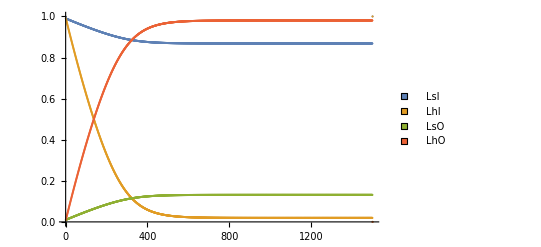

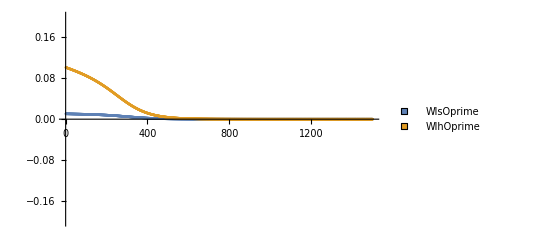

```mathematica
ListPlot[{lsItab,lhItab,lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLegends->PointLegend[{LsI,LhI,LsO,LhO},LegendMarkers->Graphics[Rectangle[]]]] 
ListPlot[{DlsOtab,DlhOtab},PlotRange->{All,{-0.2,0.2}},PlotLegends->PointLegend[{WlsOprime,WlhOprime},LegendMarkers->Graphics[Rectangle[]]]]
```